# Flood Trends Analysis

## Global and Slovenian Floods Data Insights (1750-2010)

Aleksandar Obrovac

Fakulteta za matematiko in fiziko smer Praktična matematika

30.8.2024

## Data Import and Basic Manipulation

### Importing Data

```mathematica
globalFloods=Import["C:\\Users\\Hasnain\\OneDrive\\Desktop\\fiver_project_2\\global_floods.csv"]
sloveniaFloods=Import["C:\\Users\\Hasnain\\OneDrive\\Desktop\\fiver_project_2\\Slovenia_floods.csv"]
```

{{Global occurance of floods,yearly},{Source: https://ourworldindata.org/natural-disasters},{Base Period: 1970-2023},{},{Year,Number of floods},{1970,31},{1971,15},{1972,15},{1973,20},{1974,18},{1975,17},{1976,16},{1977,47},{1978,47},{1979,34},{1980,39},{1981,41},{1982,48},{1983,49},{1984,46},{1985,57},{1986,49},{1987,66},{1988,75},{1989,46},{1990,60},{1991,76},{1992,59},{1993,84},{1994,88},{1995,93},{1996,95},{1997,96},{1998,96},{1999,123},{2000,156},{2001,156},{2002,173},{2003,159},{2004,134},{2005,191},{2006,232},{2007,219},{2008,174},{2009,159},{2010,189},{2011,160},{2012,141},{2013,149},{2014,139},{2015,166},{2016,164},{2017,129},{2018,128},{2019,195},{2020,206},{2021,222},{2022,181},{2023,166}}

{{�tevilo bliskovitih poplav v Sloveniji od leta 1750 - 2010},{},{Source: https://www.researchgate.net/profile/Tajan-Trobec/publication/322267744_Frequency_and_seasonality_of_flash_floods_in_Slovenia/links/5a4f688e0f7e9bbfacfd0010/Frequency-and-seasonality-of-flash-floods-in-Slovenia.pdf},{OBDOBJE; �tevilo bliskovitih poplav v tem obdobju},{1750 - 1770; 1},{1771 - 1790; 0},{1791 - 1810; 1},{1811 - 1830; 1},{1831 - 1850; 1},{1851 - 1870; 3},{1871 - 1890; 10},{1891 - 1910; 14},{1911 - 1930; 12},{1931 - 1950; 9},{1951 - 1970; 23},{1971 - 1990; 27},{1991 - 2010; 27}}

### Cleaning and Structuring Data

This data includes metadata and column headers that need to be removed. The core data starts from a specific index in the list.

#### For Global Floods Data

Skip Metadata:
Metadata and headers are usually in the first few entries, so start extracting from the relevant index.

```mathematica
globalFloodsData=globalFloods[[6;;]](*Skip metadata and headers*)
```

{{1970,31},{1971,15},{1972,15},{1973,20},{1974,18},{1975,17},{1976,16},{1977,47},{1978,47},{1979,34},{1980,39},{1981,41},{1982,48},{1983,49},{1984,46},{1985,57},{1986,49},{1987,66},{1988,75},{1989,46},{1990,60},{1991,76},{1992,59},{1993,84},{1994,88},{1995,93},{1996,95},{1997,96},{1998,96},{1999,123},{2000,156},{2001,156},{2002,173},{2003,159},{2004,134},{2005,191},{2006,232},{2007,219},{2008,174},{2009,159},{2010,189},{2011,160},{2012,141},{2013,149},{2014,139},{2015,166},{2016,164},{2017,129},{2018,128},{2019,195},{2020,206},{2021,222},{2022,181},{2023,166}}

The globalFloodsData variable will now contain a list of pairs {year, number of floods}.

#### For Slovenia Floods Data

Skip Metadata:
Metadata and headers are included, so start extracting the actual data.

```mathematica
(*Skip metadata and headers*)
sloveniaFloodsRaw=sloveniaFloods[[5;;]]
```

{{1750 - 1770; 1},{1771 - 1790; 0},{1791 - 1810; 1},{1811 - 1830; 1},{1831 - 1850; 1},{1851 - 1870; 3},{1871 - 1890; 10},{1891 - 1910; 14},{1911 - 1930; 12},{1931 - 1950; 9},{1951 - 1970; 23},{1971 - 1990; 27},{1991 - 2010; 27}}

```mathematica
sloveniaFloodsRaw=sloveniaFloods[[5;;]](*Skip metadata and headers*)
```

{{1750 - 1770; 1},{1771 - 1790; 0},{1791 - 1810; 1},{1811 - 1830; 1},{1831 - 1850; 1},{1851 - 1870; 3},{1871 - 1890; 10},{1891 - 1910; 14},{1911 - 1930; 12},{1931 - 1950; 9},{1951 - 1970; 23},{1971 - 1990; 27},{1991 - 2010; 27}}

Preprocessing Slovenia Floods Data:

Step 1: Split the strings by “ - “ and  “; “

```mathematica
sloveniaFloodsSplit=Map[StringSplit[#,{" - ","; "}]&,sloveniaFloodsRaw]
```

{{{1750,1770,1}},{{1771,1790,0}},{{1791,1810,1}},{{1811,1830,1}},{{1831,1850,1}},{{1851,1870,3}},{{1871,1890,10}},{{1891,1910,14}},{{1911,1930,12}},{{1931,1950,9}},{{1951,1970,23}},{{1971,1990,27}},{{1991,2010,27}}}

Step 2: Flatten the nested lists

```mathematica
sloveniaFloodsFlattened=Flatten[sloveniaFloodsSplit,1]
```

{{1750,1770,1},{1771,1790,0},{1791,1810,1},{1811,1830,1},{1831,1850,1},{1851,1870,3},{1871,1890,10},{1891,1910,14},{1911,1930,12},{1931,1950,9},{1951,1970,23},{1971,1990,27},{1991,2010,27}}

Step 3: Convert to numerical values.

```mathematica
sloveniaFloodsData=sloveniaFloodsFlattened/. {s_String:>ToExpression[s]}
```

{{1750,1770,1},{1771,1790,0},{1791,1810,1},{1811,1830,1},{1831,1850,1},{1851,1870,3},{1871,1890,10},{1891,1910,14},{1911,1930,12},{1931,1950,9},{1951,1970,23},{1971,1990,27},{1991,2010,27}}

The sloveniaFloodsData variable now contain list of pairs {starting_year, ending_year, number of floods}.

## Visualizations

### For Global Data:

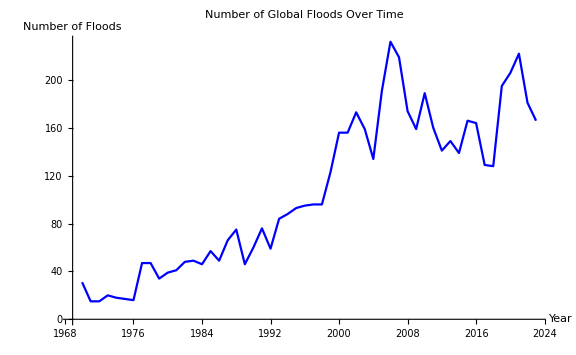

```mathematica
ListLinePlot[globalFloodsData,PlotLabel->"Number of Global Floods Over Time",AxesLabel->{"Year","Number of Floods"},PlotStyle->Blue, ImageSize->Large]
```

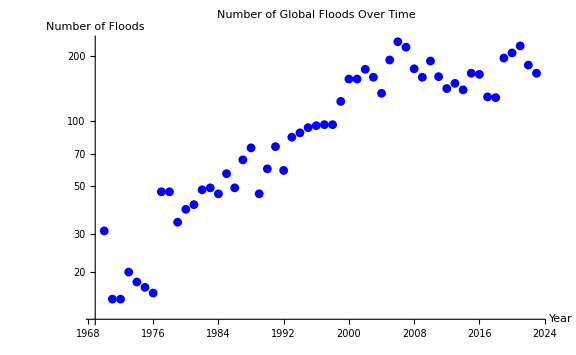

```mathematica
ListLogPlot[globalFloodsData,PlotLabel->"Number of Global Floods Over Time",AxesLabel->{"Year","Number of Floods"},PlotStyle->Blue, ImageSize->Large]
```

To show the distribution of flood counts, we will create a histogram

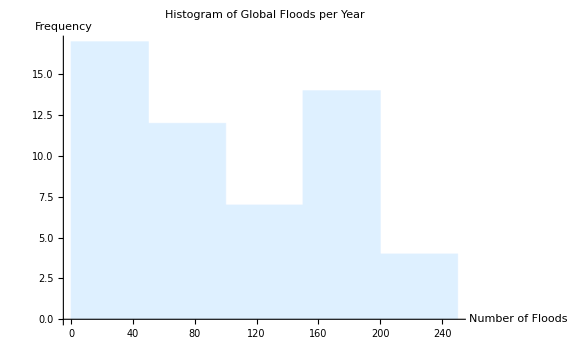

```mathematica
floodsData=globalFloodsData[[All,2]];

Histogram[floodsData,PlotLabel->"Histogram of Global Floods per Year",AxesLabel->{"Number of Floods","Frequency"},ChartStyle->LightBlue, ImageSize->Large]
```

### For Slovenia Data:

In Slovenia data each entry represents a range of years. We can use the midpoint of each range for time series plots.

```mathematica
sloveniaFloodsMidpoints=N[Map[{Mean[Take[#,2]],Last[#]}&,sloveniaFloodsData]]
```

{{1760.,1.},{1780.5,0.},{1800.5,1.},{1820.5,1.},{1840.5,1.},{1860.5,3.},{1880.5,10.},{1900.5,14.},{1920.5,12.},{1940.5,9.},{1960.5,23.},{1980.5,27.},{2000.5,27.}}

Below is a List Line Plot that shows the number of floods in Slovenia over time, highlighting variations in flood frequency.

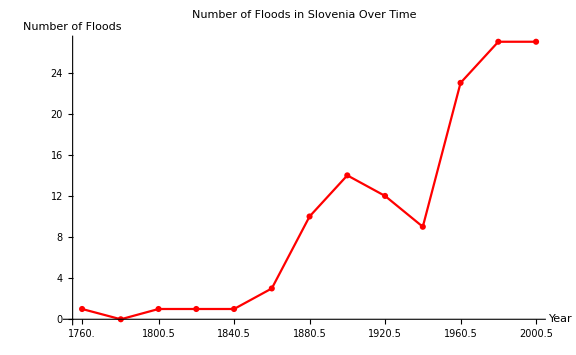

```mathematica
ListLinePlot[sloveniaFloodsMidpoints,PlotStyle->RGBColor[1,0,0],PlotMarkers->Automatic,PlotLabel->"Number of Floods in Slovenia Over Time",AxesLabel->{"Year","Number of Floods"},Ticks->{sloveniaFloodsMidpoints[[All,1]],Automatic},ImageSize->Large,Joined->True]
```

A cumulative plot shows the total number of floods up to each time point, giving insight into how the frequency of floods has changed over time.

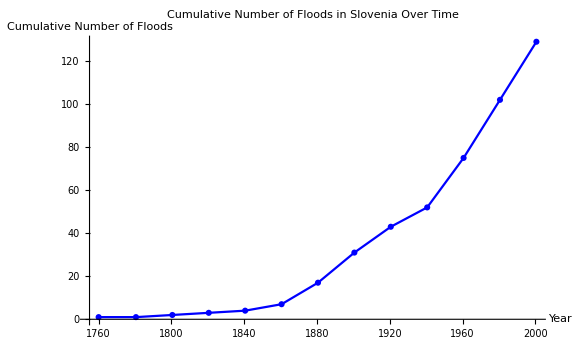

```mathematica
cumulativeFloods=Accumulate[sloveniaFloodsMidpoints[[All,2]]];
ListLinePlot[Transpose[{sloveniaFloodsMidpoints[[All,1]],cumulativeFloods}],PlotStyle->RGBColor[0,0,1],PlotMarkers->Automatic,PlotLabel->"Cumulative Number of Floods in Slovenia Over Time",AxesLabel->{"Year","Cumulative Number of Floods"},ImageSize->Large,Joined->True]
```

A BarChart showing the number of floods in Slovenia across different time intervals, illustrating the frequency of flood occurrences over the centuries

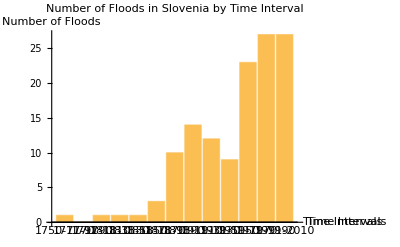

```mathematica
BarChart[{1,0,1,1,1,3,10,14,12,9,23,27,27},ChartLabels->Placed[{"1750-1770","1771-1790","1791-1810","1811-1830","1831-1850","1851-1870","1871-1890","1891-1910","1911-1930","1931-1950","1951-1970","1971-1990","1991-2010"},Below],PlotLabel->"Number of Floods in Slovenia by Time Interval",AxesLabel->{"  Time Intervals","Number of Floods"}, ImageSize->Full]
```

## Analysis

### Define Custom Functions

Defining some custom functions that can help us analyze and manipulate the data more effectively.

#### Calculate Yearly Flood Rate in Slovenia for specific Time Interval:

To analyze the flood data in Slovenia, we need to calculate the average yearly flood rate for each specified time interval. This calculation helps us understand how the frequency of floods in Slovenia has changed over time, which is crucial for identifying trends and patterns.
Defining the function:

```mathematica
averageFloodRateInSlovenia[{startYear_,endYear_,floods_}]:=Module[{duration},duration=endYear-startYear+1;
{startYear,endYear,floods,N[floods/duration]}]
```

Applying the function

```mathematica
sloveniaFloodsWithRates=Map[averageFloodRateInSlovenia,sloveniaFloodsData]
```

{{1750,1770,1,0.047619},{1771,1790,0,0.},{1791,1810,1,0.05},{1811,1830,1,0.05},{1831,1850,1,0.05},{1851,1870,3,0.15},{1871,1890,10,0.5},{1891,1910,14,0.7},{1911,1930,12,0.6},{1931,1950,9,0.45},{1951,1970,23,1.15},{1971,1990,27,1.35},{1991,2010,27,1.35}}

The fourth element in each list of output is the average yearly flood rate, indicating the average number of floods per year during that interval.
Creating a table of output:

```mathematica
Grid[
Prepend[
sloveniaFloodsWithRates,
{"Start Year","End Year","Total Floods","Average Yearly Flood Rate"}
],
Frame->All,
Background->{None,{LightGray,{White}}},
Alignment->Center
]
```

Start Year | End Year | Total Floods | Average Yearly Flood Rate
1750 | 1770 | 1 | 0.047619
1771 | 1790 | 0 | 0.
1791 | 1810 | 1 | 0.05
1811 | 1830 | 1 | 0.05
1831 | 1850 | 1 | 0.05
1851 | 1870 | 3 | 0.15
1871 | 1890 | 10 | 0.5
1891 | 1910 | 14 | 0.7
1911 | 1930 | 12 | 0.6
1931 | 1950 | 9 | 0.45
1951 | 1970 | 23 | 1.15
1971 | 1990 | 27 | 1.35
1991 | 2010 | 27 | 1.35

#### Calculate Overall Average Number of Floods per Year in Slovenia (1750-2010)

This function calculates the average number of floods per year across the entire time period from 1750 to 2010 in Slovenia. It provides insight into the general frequency of floods over the given historical range. The average is computed by dividing the total number of floods by the total number of years represented in the dataset.
Defining the function to calculate average number of floods per year in Slovenia.

```mathematica
averageFloodsPerYear[data_List]:=Module[{totalFloods,totalYears},totalFloods=Total[data[[All,3]]];
totalYears=Total[(data[[All,2]]-data[[All,1]]+1)];
N[totalFloods/totalYears]]
```

Applying the function on Slovenia floods data.

```mathematica
averageFloodsPerYear[sloveniaFloodsData]
```

0.494253

The average number of floods per year over this time period is around 0.494, indicating that, on average, there is slightly less than one flood per year in Slovenia

#### Compare Global vs. Slovenia Flood Rates:

This function will compare the number of floods in a given year globally with the average flood rate in Slovenia for the corresponding time period.
Defining the function.

```mathematica
compareFloodRates[sloveniaData_,globalData_,startYear_,endYear_]:=
Module[{sloveniaSelected,globalSelected,sloveniaAvg,globalAvg},
(*Select the relevant data for Slovenia and Global floods based on the specified period*)
sloveniaSelected=
Select[sloveniaData,#[[1]]>=startYear&&#[[2]]<=endYear&];
globalSelected=
Select[globalData,#[[1]]>=startYear&&#[[1]]<=endYear&];
(*Calculate the average flood rates for the selected periods*)
sloveniaAvg=averageFloodsPerYear[sloveniaSelected];    (* Pre defined custom function averageFloodsPerYear *)
globalAvg=N[Mean[globalSelected[[All,2]]]];
(*Return the results as a list of averages*)
{sloveniaAvg,globalAvg}]
```

The compareFloodRates function compares flood rates between Slovenia and global data for a specified time period. It filters the datasets to include only records within the given range, then calculates the average number of floods per year for both Slovenia and the global dataset. The function returns these averages as a list, allowing for direct comparison of flood frequencies over the specified period.

The specific time period from 1970 to 2010 is chosen because it provides a common range that overlaps between the global and Slovenian datasets.

```mathematica
{averageSloveniaRate, averageGlobalRate} = 
  N[compareFloodRates[sloveniaFloodsData, globalFloodsData, 1970, 2010]]
```

{1.35,87.5122}

The result {1.35, 87.5122} indicates that:

Slovenia experienced an average of 1.35 floods per year from 1970 to 2010.
Globally, the average number of floods per year during the same period was approximately 87.51.

This comparison shows that while Slovenia has a relatively lower average flood rate, the global flood rate is significantly higher, reflecting the larger scale and frequency of flood events worldwide.

### Statistical Analysis: Mean and Standard Deviation

To understand the central tendency and variability of flood occurrences.

#### Global Data:

```mathematica
globalFloodsMean=N[Mean[globalFloodsData[[All,2]]]];
globalFloodsStdDev=N[StandardDeviation[globalFloodsData[[All,2]]]];
```

#### Slovenia Data:

```mathematica
sloveniaFloodsMean=N[Mean[sloveniaFloodsData[[All,3]]]];
sloveniaFloodsStdDev=N[StandardDeviation[sloveniaFloodsData[[All,3]]]];
```

#### Results:

Create a Table to Display the Results

```mathematica
(*Define the data*)
floodsStatistics={{"Global Floods",globalFloodsMean,globalFloodsStdDev},{"Slovenia Floods",sloveniaFloodsMean,sloveniaFloodsStdDev}};

(*Create the table*)
Grid[
Prepend[floodsStatistics,{"Dataset","Mean","Standard Deviation"}],
Frame->All,
Background->{None,{LightGray,{White}}},
Alignment->Center
]
```

Dataset | Mean | Standard Deviation
Global Floods | 106.185 | 64.7162
Slovenia Floods | 9.92308 | 10.1691